## Standard Ricker model EWS

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Google\ Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_std"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=-0.2;
bh=1;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="trans_r_long";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/"<>simName<>"/ktau.csv"];
```

```mathematica
numSims=Length[dfKtau]-1
```

100

```mathematica
(* Realisation number to display *)
displayNum=2;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean}

```mathematica
trajVals=Cases[dfEws[[2;;,{1,3,4}]],{displayNum,_,_}][[;;,{2,3}]];
```

```mathematica
(* Extract info of one trajectory *)
trajVals=Cases[dfEws[[2;;,{1,3,4}]],{displayNum,_,_}][[;;,{2,3}]];
tVals = trajVals[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
```

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[trajVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
AxesLabel->{"t","x(t)"},
PlotRange->{{0,tmax},All}];
```

### Plot format adjustment

```mathematica
rTicks=Round[Range[bh,bl,-0.2],0.1];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

```mathematica
rTicks
```

{1.,0.8,0.6,0.4,0.2,0.,-0.2}

```mathematica
plotTraj=Show[plotX,
PlotRange->{{0,tmax},{0,170}},
ImageSize->imgs,
LabelStyle->ls,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Growth rate, r"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Arrowheads[{-aHeadSize,aHeadSize}*0.7],
Thickness[0.002],
Arrow[{Scaled[{0,0.2},{0,0}],Scaled[{0,0.2},{windowComps*dt2,0}]}]
}
];
```

## EWS Plots

### Variance

```mathematica
(* plot colour *)
colVar=TMBcolours[[2]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
varEws=Table[Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],{realNum,1,numSims}];
```

```mathematica
varEws//Dimensions
```

{5,400,2}

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotVar=ListLinePlot[varEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}];
```

### Coefficient of variation

```mathematica
(* plot colour *)
colCV=TMBcolours[[3]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
cvEws=Table[Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],{realNum,1,numSims}];
```

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotCv=ListLinePlot[cvEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colCV,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}];
```

### Smax/Mean

```mathematica
(* plot colour *)
colSmaxMean=TMBcolours[[4]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Mean"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxMeanEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSmaxMean=ListPlot[smaxMeanEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxMean,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["S_max/<X>",ls],textPos,{-1,0}]}];
```

### Smax/Var

```mathematica
(* plot colour *)
colSmaxVar=TMBcolours[[5]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxVarEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSmaxVar=ListPlot[smaxVarEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["S_max/Variance",ls],textPos,{-1,0}]}];
```

### Skewness

```mathematica
(* plot colour *)
colSkew=TMBcolours[[5]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Skewness"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxVarEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

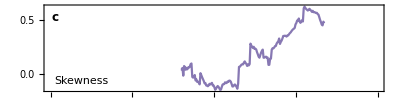

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSkew=ListPlot[smaxVarEws[[1]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Autocorrelation (combined)

```mathematica
(* plot colour *)
colAC=TMBcolours[[{4,5,7}]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],#][[1,1]]&/@{"Lag-1 AC","Lag-2 AC","Lag-3 AC"};
```

```mathematica
(* Construct relevant sub dataframe *)
acEws=Table[Cases[dfEws[[2;;,{1,3,indexEws[[i]]}]],{realNum,_,_}][[;;,{2,3}]],{realNum,1,numSims},{i,1,3}];
```

```mathematica
acEws//Dimensions
```

{5,3,400,2}

```mathematica
(* line legend *)
legend=LineLegend[colAC,Table["lag-"<>ToString[i],{i,{1,2,3}}],Spacings->{0,0.2},LabelStyle->(ls-1)]
```

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotAC=ListLinePlot[acEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
PlotRange->{{0,tmax},All},
PlotStyle->colAC,
Axes->False,
PlotLegends->Placed[legend,{0.15,0.65}],
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Autocorrelation",ls],textPos,{-1,0}]}];
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

```mathematica
stateVals={"x"};
```

### Variance

```mathematica
indexKtau=Position[dfKtau[[1]],"Variance"][[1,1]]
```

5

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | -0.969091 | -0.97961 | -0.958052 | -0.985714 | -0.965584 | -0.975455 | -0.941039 | -0.977532 | -0.944156 | -0.968442 | -0.970519 | -0.976104 | -0.991429 | -0.978052 | -0.960779 | -0.975844 | -0.966753 | -0.986234 | -0.942078 | -0.981558 | -0.975584 | -0.982078 | -0.952857 | -0.955714 | -0.95 | -0.984026 | -0.973636 | -0.965065 | -0.982987 | -0.983636 | -0.985584 | -0.984545 | -0.966364 | -0.978052 | -0.931039 | -0.97026 | -0.953247 | -0.983896 | -0.985584 | -0.976753 | -0.974805 | -0.986623 | -0.941299 | -0.974545 | -0.936883 | -0.964026 | -0.939221 | -0.948312 | -0.954805 | -0.957013 | -0.99 | -0.97 | -0.991299 | -0.963636 | -0.967662 | -0.991299 | -0.986494 | -0.97013 | -0.973636 | -0.954675 | -0.961169 | -0.967922 | -0.986494 | -0.98 | -0.982078 | -0.976364 | -0.981558 | -0.976104 | -0.955584 | -0.986623 | -0.981169 | -0.975065 | -0.988442 | -0.975974 | -0.986883 | -0.961688 | -0.983766 | -0.976753 | -0.964156 | -0.96961 | -0.968442 | -0.969221 | -0.973766 | -0.964156 | -0.984156 | -0.976234 | -0.973377 | -0.967792 | -0.967403 | -0.970779 | -0.982727 | -0.977922 | -0.957403 | -0.958312 | -0.981948 | -0.975584 | -0.923247 | -0.96961 | -0.984286 | -0.983636

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colVar,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

12

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | 0.655844 | -0.279221 | -0.0225974 | -0.258312 | 0.456104 | 0.896364 | 0.779351 | -0.516753 | 0.431429 | 0.77039 | 0.255974 | -0.597143 | 0.205584 | 0.555714 | -0.101948 | -0.450779 | 0.511039 | -0.0719481 | 0.427013 | 0.804545 | 0.16026 | 0.246623 | 0.198182 | 0.452208 | -0.465974 | 0.055974 | 0.805325 | 0.421948 | -0.485455 | 0.344286 | 0.490519 | 0.0668831 | 0.823377 | -0.171948 | 0.325455 | -0.048961 | -0.0284416 | 0.332987 | 0.369351 | 0.476753 | 0.264416 | -0.208831 | 0.365325 | 0.100909 | 0.428831 | 0.186753 | -0.16039 | 0.448701 | 0.223896 | 0.537532 | -0.176753 | 0.544545 | 0.139091 | 0.785195 | -0.701039 | 0.673247 | -0.575584 | 0.369221 | -0.238182 | 0.832727 | -0.192987 | 0.406364 | 0.144286 | 0.167792 | 0.286234 | 0.310909 | -0.594675 | 0.303636 | -0.302857 | 0.603896 | 0.0271429 | 0.633247 | 0.36961 | 0.359481 | -0.0962338 | 0.688182 | 0.493247 | 0.486494 | 0.815065 | 0.900519 | -0.788442 | 0.259221 | 0.77987 | 0.701948 | -0.240519 | 0.388052 | 0.166234 | -0.0511688 | -0.0787013 | 0.660519 | -0.141818 | -0.414416 | 0.714935 | -0.636623 | 0.706753 | 0.194286 | -0.528182 | 0.414545 | -0.203766 | -0.085974

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colSmaxMean,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
indexKtau=Position[dfKtau[[1]],"Coefficient of variation"][[1,1]]
```

10

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | 0.941169 | 0.90026 | 0.911169 | 0.517403 | 0.77 | 0.939351 | 0.917273 | 0.633766 | 0.959221 | 0.658182 | 0.850649 | 0.808961 | 0.634805 | 0.646234 | 0.873247 | 0.886883 | 0.944416 | 0.503377 | 0.906753 | 0.877532 | 0.781688 | 0.728701 | 0.884156 | 0.866364 | 0.847792 | 0.790779 | 0.887143 | 0.874416 | 0.919221 | 0.71974 | 0.907792 | 0.716883 | 0.852987 | 0.711558 | 0.946623 | 0.858571 | 0.936104 | 0.775325 | 0.907403 | 0.932857 | 0.943896 | 0.586234 | 0.913506 | 0.772468 | 0.945844 | 0.921948 | 0.843117 | 0.918571 | 0.927143 | 0.933636 | 0.604286 | 0.825065 | 0.179351 | 0.931688 | 0.917922 | -0.00779221 | 0.895065 | 0.79039 | 0.916494 | 0.872727 | 0.768571 | 0.922857 | 0.299091 | 0.785325 | 0.776623 | 0.722987 | 0.931948 | 0.931688 | 0.89039 | 0.758571 | 0.430779 | 0.621169 | 0.850909 | 0.827792 | 0.866883 | 0.867143 | 0.652597 | 0.680519 | 0.883636 | 0.887273 | 0.964156 | 0.873247 | 0.862468 | 0.869221 | 0.851169 | 0.850519 | 0.713636 | 0.655844 | 0.786883 | 0.943247 | 0.712078 | 0.864675 | 0.949481 | 0.938312 | 0.936494 | 0.916494 | 0.961948 | 0.825844 | 0.818052 | 0.473636

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colCV,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax"][[1,1]]
```

9

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | -0.333333 | -0.944444 | 0.111111 | -0.833333 | -0.722222 | -0.166667 | -0.111111 | -0.722222 | -0.222222 | -0.222222 | -0.944444 | -0.944444 | -0.777778 | -0.722222 | 0.777778 | -0.0555556 | -0.611111 | -0.888889 | -0.444444 | -0.611111 | 0.166667 | -0.333333 | -0.888889 | -0.777778 | -0.777778 | -0.888889 | -0.166667 | -0.388889 | -0.722222 | -0.833333 | -0.833333 | -0.777778 | -0.611111 | -0.777778 | -0.333333 | -0.944444 | -0.277778 | -0.833333 | -0.888889 | -0.833333 | -0.0555556 | -0.944444 | -0.777778 | -0.944444 | -0.277778 | 0.5 | -0.5 | -0.777778 | -0.666667 | -0.777778 | -0.833333 | -0.722222 | -1. | 0.166667 | -0.166667 | -0.888889 | -0.888889 | -0.833333 | -0.888889 | -0.722222 | -0.388889 | -0.444444 | -0.944444 | -0.833333 | -0.833333 | -0.777778 | -0.722222 | -0.888889 | -0.833333 | -0.722222 | -0.888889 | -1. | -0.0555556 | -0.833333 | -0.111111 | -0.388889 | -0.833333 | -0.944444 | 0.277778 | 0.0555556 | -0.5 | -0.833333 | -0.833333 | -0.722222 | -0.833333 | -0.5 | -0.888889 | -0.888889 | -0.666667 | -0.333333 | -1. | -0.833333 | -0.277778 | -0.555556 | 0.222222 | -0.333333 | -0.777778 | -0.888889 | -1. | -0.888889

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colSmaxMean,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax/Var"][[1,1]]
```

11

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | 0.944444 | 0.722222 | 0.888889 | 0.833333 | 0.944444 | 0.555556 | 0.555556 | 0.166667 | 0.888889 | 0.944444 | 0.944444 | -0.277778 | 0.277778 | 0.888889 | 0.944444 | 0.777778 | 0.222222 | 0.388889 | 0.944444 | 0.777778 | 0.833333 | 0.888889 | 0.444444 | 0.888889 | 0.944444 | 0.777778 | 0.833333 | 0.666667 | 0.722222 | 0.777778 | 0.888889 | 0.722222 | 0.555556 | 0.944444 | 1. | 0.888889 | 1. | 0.888889 | 0.388889 | 0.777778 | 1. | 0.722222 | 0.833333 | 0.722222 | 0.611111 | 0.833333 | 0.666667 | 0.888889 | 0.722222 | 0.222222 | 0.277778 | 0.722222 | -0.0555556 | 1. | 0.777778 | 0.333333 | 0.611111 | 0.777778 | 0.666667 | 0.611111 | 0.777778 | 0.944444 | 0.5 | 0.833333 | 0.888889 | 0.333333 | 0.777778 | 0.833333 | 0.777778 | 0.333333 | 0.444444 | 0.277778 | 0.888889 | 0.666667 | 0.833333 | 0.888889 | 0.777778 | 0.777778 | 0.944444 | 0.944444 | 0.944444 | 0.833333 | 0.833333 | 0.222222 | 0.777778 | 0.833333 | 0.5 | 0.388889 | 0.777778 | 0.777778 | 0.444444 | 0.888889 | 0.611111 | 0.888889 | 1. | 0.611111 | 0.888889 | 0.611111 | 0.444444 | 0.

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colSmaxVar,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}];
```

### Skew

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

12

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | 0.655844 | -0.279221 | -0.0225974 | -0.258312 | 0.456104 | 0.896364 | 0.779351 | -0.516753 | 0.431429 | 0.77039 | 0.255974 | -0.597143 | 0.205584 | 0.555714 | -0.101948 | -0.450779 | 0.511039 | -0.0719481 | 0.427013 | 0.804545 | 0.16026 | 0.246623 | 0.198182 | 0.452208 | -0.465974 | 0.055974 | 0.805325 | 0.421948 | -0.485455 | 0.344286 | 0.490519 | 0.0668831 | 0.823377 | -0.171948 | 0.325455 | -0.048961 | -0.0284416 | 0.332987 | 0.369351 | 0.476753 | 0.264416 | -0.208831 | 0.365325 | 0.100909 | 0.428831 | 0.186753 | -0.16039 | 0.448701 | 0.223896 | 0.537532 | -0.176753 | 0.544545 | 0.139091 | 0.785195 | -0.701039 | 0.673247 | -0.575584 | 0.369221 | -0.238182 | 0.832727 | -0.192987 | 0.406364 | 0.144286 | 0.167792 | 0.286234 | 0.310909 | -0.594675 | 0.303636 | -0.302857 | 0.603896 | 0.0271429 | 0.633247 | 0.36961 | 0.359481 | -0.0962338 | 0.688182 | 0.493247 | 0.486494 | 0.815065 | 0.900519 | -0.788442 | 0.259221 | 0.77987 | 0.701948 | -0.240519 | 0.388052 | 0.166234 | -0.0511688 | -0.0787013 | 0.660519 | -0.141818 | -0.414416 | 0.714935 | -0.636623 | 0.706753 | 0.194286 | -0.528182 | 0.414545 | -0.203766 | -0.085974

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colSmaxVar,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-1 Autocorrelation

```mathematica
indexKtau1=Position[dfKtau[[1]],"Lag-1 AC"][[1,1]];
indexKtau2=Position[dfKtau[[1]],"Lag-2 AC"][[1,1]];
indexKtau3=Position[dfKtau[[1]],"Lag-3 AC"][[1,1]];
```

```mathematica
ktauVals1=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau1}]],{state,_}][[;;,2]],state],{state,stateVals}];
ktauVals2=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau2}]],{state,_}][[;;,2]],state],{state,stateVals}];
ktauVals3=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau3}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
(* Box plot *)
boxAc=BoxWhiskerChart[{ktauVals1[[;;,2;;]][[1]],ktauVals2[[;;,2;;]][[1]],ktauVals3[[;;,2;;]][[1]]},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colAC,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
Clear[colFun1]
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
specTimes=Union[dfPspec[[2;;,3]]]
```

{159.,179.,199.,219.,239.,259.,279.,299.,319.}

```mathematica
(* time values to plot power spectrum *)
plotTimes = specTimes[[1;;-1;;3]]
```

{159.,219.,279.}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,_,timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
specData//Dimensions
```

{3,41,2}

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean}

```mathematica
(* Power spectra normalised by the variance *)
varianceVals=Table[Cases[dfEws[[2;;,{1,2,3,7}]],{displayNum,"x",Round[time],_}][[1,4]],{time,plotTimes}];
specNormData=specData;
specNormData[[;;,;;,2]]=specNormData[[;;,;;,2]]/varianceVals;
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
timeRange
```

{159.,339.}

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{colFun1[(#-199)/(309-199)]&,timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->{-2,10},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Range[0,10,2]},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}];
```

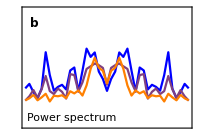

```mathematica
(* normalised power spectrum plot *)
plotPspecNorm=ListLinePlot[specNormData,
PlotRange->{-0.2,1},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Range[0,1,0.2]},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAC,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAc,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspecNorm,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

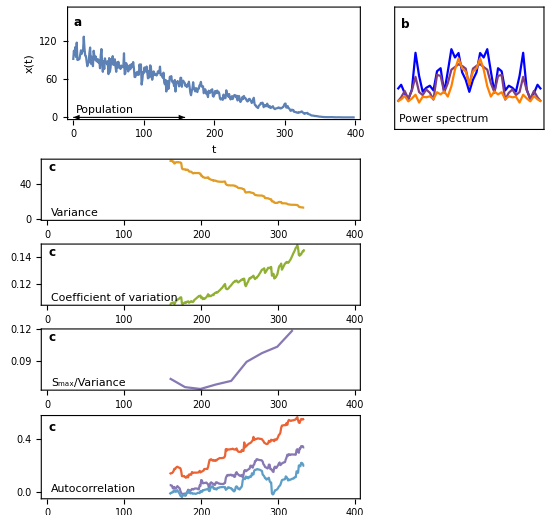

```mathematica
plotGrid
```

```mathematica
(*Export["figures/single_"<>simName<>".png",plotGrid,ImageResolution->200];*)
```